```mathematica
(* Import data from Johns Hopkins *)
HopkinsConfirmed = Drop[Import[NotebookDirectory[]<>"/johns-hopkins-data/time_series_covid19_confirmed_US.csv",CharacterEncoding->"UTF8"],1];
HopkinsDeaths = Drop[Import[NotebookDirectory[]<>"/johns-hopkins-data/time_series_covid19_deaths_US.csv",CharacterEncoding->"UTF8"],1];
StateList=AlphabeticSort[DeleteDuplicates[Transpose[HopkinsConfirmed][[7]]]];
(*Export[NotebookDirectory[]<>"/US-states.xls",TableForm[Table[{i,StateList[[i]]},{i,1,Length[StateList]}]],"XLS"];*)
```

```mathematica
(* Data for countries can be split over multiple rows in the data from Hopkins *)
DataByState = Table[{},{i,1,Length[StateList]}];
NumberOfDays = Length[Transpose[HopkinsConfirmed]]-11;

For[state = 1, state ≤ Length[StateList],state++,
TempConfirmed=Table[0,{i,1,NumberOfDays}];
TempDeaths = Table[0,{i,1,NumberOfDays}];
For[row=1,row≤ Length[HopkinsConfirmed],row++,
If[StringMatchQ[StateList[[state]], HopkinsConfirmed[[row,7]]],
(* state name of ConfirmedBystate matches current row *)
TempConfirmed = TempConfirmed + Drop[HopkinsConfirmed[[row]],11];
]
];
For[row=1,row≤ Length[HopkinsDeaths],row++,
If[StringMatchQ[StateList[[state]], HopkinsDeaths[[row,7]]],
(* state name of ConfirmedBystate matches current row *)
TempDeaths = TempDeaths + Drop[HopkinsDeaths[[row]],12];
]
];

TempConfirmedDiff=TempConfirmed-Drop[Join[{0},TempConfirmed],-1];
TempDeathsDiff=TempDeaths-Drop[Join[{0},TempDeaths],-1];
DataByState[[state]]= {ToString[StateList[[state]]],TempConfirmed,TempDeaths,TempConfirmedDiff,TempDeathsDiff};
];
(* Model *)
SIR[state_,dday_] := (
n=n0;
e=e0;
i=i0;
r=0;
m=0;
c=i+r+m;
s = n-e-i-r-m;
cost = 0;
For[sirday=1,sirday≤ dday, sirday++,
lambda = (gamma + delta) * listr0[[sirday]][[2]];
ds = -lambda i *(s/n);
de=lambda i * (s/n)-epsilon e;
di = epsilon e * (s/n) -gamma i - delta i;
inew = lambda i * (s/n);
dr = gamma i;
dm = delta i;
dc=di +dr+dm;
s+=ds;
e+=de;
i+=di;
r+=dr;
m+=dm;
c+=dc;
n=s+e+i+r;
risk=i*listr0[[sirday]][[2]];
If[sirday≤ Length[DataByState[[state]][[2]]],
cost = cost + (c-DataByState[[state]][[2]][[sirday]])^2;];
];
Return[{s,i,r,m,c,cost,di,dm,inew,risk}];
);
```

```mathematica
Window =3;(* Number of days over which to fit the model *)
future=30; (* Number of days to project ahead *)
```

```mathematica
StateSIR[state_] := (
Currentstate =state;
today = Length[DataByState[[Currentstate]][[2]]];
CFR=DataByState[[Currentstate]][[3]][[-1]]/(DataByState[[Currentstate]][[2]][[-1]]+1);

n0 = 10000000;
e0=5;
i0=5;
epsilon=1/2;
gamma=(1-CFR)/12.4;
delta = CFR/10.4;
listr0 = {};
For[day = 1, day <= Length[DataByState[[Currentstate]][[2]]] + future, day++,
  listr0 = Join[listr0, {{day, 4.3}}];
  ];
(* Fit model to the data *)
For[day=1,day≤Length[DataByState[[Currentstate]][[2]]]-Window,day++,
bestr0=listr0[[day]][[2]];
bestcost=SIR[Currentstate,day+Window][[6]];
For[kr0 = 0.1,kr0≤20,kr0=kr0+0.1,
(* set this possible r0 for all following days and see what the cost is *)
For[j = 0, j <= Length[listr0] - day, j++,
listr0[[day + j]][[2]] = kr0;];
temp=SIR[Currentstate,day + Window];
If[temp[[6]]<bestcost,bestcost=temp[[6]];bestr0=kr0;];
];
(* We found a good r0 for this day, set it for all the following days *)
For[j = 0, j <= Length[listr0] - day, j++,
listr0[[day + j]][[2]] =bestr0;];
];

(* Generate the lists of data for the plots *)
       lists={};
listi={};
listr={};
listm={};
listc={};
listdi={};
listdm={};
listinew = {};
listrisk={};
For[day=1,day≤Length[DataByState[[Currentstate]][[2]]]+future,day++,
temp=SIR[Currentstate,day];
lists=Append[lists,{day,temp[[1]]}];
listi=Append[listi,{day,temp[[2]]}];
listr=Append[listr,{day,temp[[3]]}];
listm=Append[listm,{day,temp[[4]]}];
listc=Append[listc,{day,temp[[5]]}];
listdi=Append[listdi,{day,temp[[7]]}];
listdm=Append[listdm,{day,temp[[8]]}];
listinew = Append[listinew,{day,temp[[9]]}];
listrisk = Append[listrisk,{day,temp[[10]]}];
];
Return[{Currentstate,DataByState[[Currentstate]][[1]],listr0,listi,listr,listm,listc,listdi,listdm,listinew,listrisk}];
);
```

```mathematica
AbsoluteTiming[StateSIR[2];]
```

{30.2569,Null}

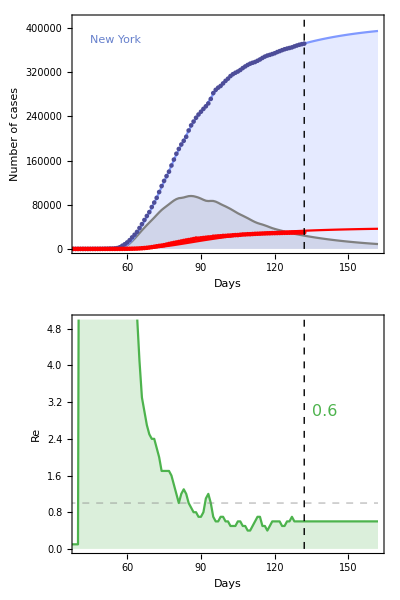

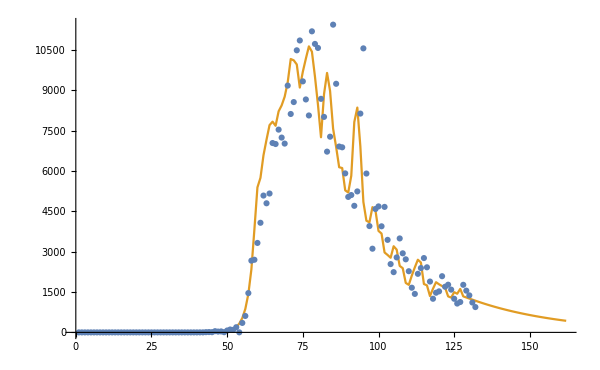

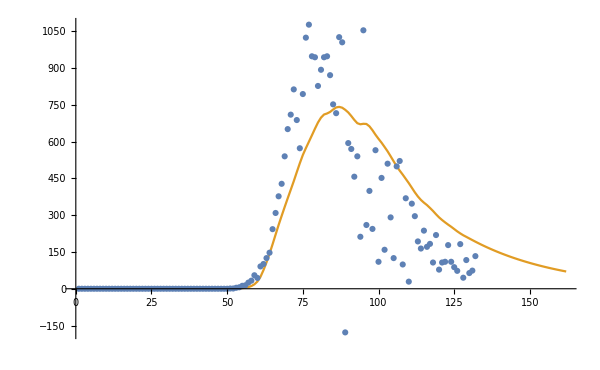

```mathematica
(* Fit model for this state *)
StateSIR[37];

(* Generate plots *)
height=Max[ {Max[Drop[listc,-future+5]],Max[DataByState[[Currentstate]][[2]]]}];

If[listr0[[-1]][[2]]<0.8,R0Color=RGBColor[0.3,0.7,0.3],If[listr0[[-1]][[2]]>1.2,R0Color=RGBColor[0.7,0.3,0.3],R0Color=RGBColor[0.9,0.7,0.3]]];

plotFinalR0 = Graphics[{Text[Style[listr0[[-1]][[2]], FontSize->16,R0Color],{today+3,3},{Left,Center}]}];

plotLine = Graphics[Style[Line[{{0, 1}, {today+future, 1}}],Dashed,RGBColor [0.5,0.5,0.5,0.5]]];

plotstatename = Graphics[{Text[Style[DataByState[[Currentstate]][[1]], Large,RGBColor[0.4,0.5,0.8]],{45,1.00height},{Left,Center}]}];

plotModel=Show[{ListPlot[{listi,listc,DataByState[[Currentstate]][[2]],DataByState[[Currentstate]][[3]],listm},PlotRange->{{40,today+future},{0,1.10height}},Joined->{True,True,False,False,True},Filling->{1-> Bottom,2->Bottom},PlotStyle->{Gray,RGBColor[0.5,0.6,1],RGBColor[0.3,0.3,0.6],Red,Red},FrameLabel->{"Days","Number of cases"},Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Thickness[0.002],13],AspectRatio->1/1,ImageSize->600],plotstatename}];

plotR0=ListPlot[listr0,Joined->True,Filling->{1->Bottom},PlotStyle->R0Color,FrameLabel->{"Days","Re"},FrameStyle->Directive[Thickness[0.002],13],Frame->True,FrameTicks->Automatic,AspectRatio->1/8,PlotRange->{{40,today+future},{0,5}},ImageSize->600];

ThePlotThickens=Multicolumn[{Show[{plotModel,Graphics[{Dashed, Line[{{today, 0}, {today, 1.2 height}}]}]},ImagePadding->{{70,10},{20,10}}],Show[{plotR0,plotFinalR0,plotLine,Graphics[{Dashed, Line[{{today, 0}, {today, 20}}]}]},ImagePadding->{{70,10},{40,5}}]},1]

stateFilename=NotebookDirectory[]<>"/results/SEIR-US-" <> ToString[DataByState[[Currentstate]][[1]]] <> "-" <> DateString[{"ISODate"}] <> ".png";

Export[stateFilename, ThePlotThickens, ImageResolution -> 600];
ListPlot[{DataByState[[Currentstate]][[4]],listinew},Joined->{False,True},PlotRange->All,ImageSize->600]
ListPlot[{DataByState[[Currentstate]][[5]],listdm},Joined->{False,True},PlotRange->All,ImageSize->600]
```

```mathematica
ResultsPerState={};
For[state=1,state≤Length[StateList],state++,
CFRTemp = {};
For[delay=1,delay≤20,delay++,CFRTemp=Append[CFRTemp,Join[Drop[DataByState[[state]][[4]],delay],Table[0,{i,1,delay}]]/DataByState[[state]][[2]]]];
meanTemp=Table[CFRTemp[[i]][[SparseArray[CFRTemp[[i]]]["NonzeroPositions"][[-1]][[1]]]],{i,1,20}];
ResultsPerState = Append[ResultsPerState,Join[StateSIR[state],{N[Mean[meanTemp]],N[MeanDeviation[meanTemp]]}]];
Print["State: "<>ResultsPerState[[-1]][[2]]<>" -> "<>ToString[ResultsPerState[[-1]][[3]][[-1]][[2]]]];
]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

State: Alabama -> 1.5

State: Alaska -> 4.1

State: American Samoa -> 0.1

State: Arizona -> 1.5

State: Arkansas -> 1.6

State: California -> 1.3

State: Colorado -> 1.

State: Connecticut -> 0.7

State: Delaware -> 0.7

State: Diamond Princess -> 0.1

State: District of Columbia -> 0.7

State: Florida -> 1.1

State: Georgia -> 1.1

State: Grand Princess -> 0.1

State: Guam -> 1.

State: Hawaii -> 0.6

State: Idaho -> 0.7

State: Illinois -> 0.7

State: Indiana -> 0.8

State: Iowa -> 0.7

State: Kansas -> 0.8

State: Kentucky -> 1.2

State: Louisiana -> 1.1

State: Maine -> 1.

State: Maryland -> 0.8

State: Massachusetts -> 1.7

State: Michigan -> 0.7

State: Minnesota -> 0.9

State: Mississippi -> 1.1

State: Missouri -> 1.2

State: Montana -> 3.9

State: Nebraska -> 0.9

State: Nevada -> 0.9

State: New Hampshire -> 1.1

State: New Jersey -> 0.6

State: New Mexico -> 0.7

State: New York -> 0.6

State: North Carolina -> 1.5

State: North Dakota -> 0.8

State: Northern Mariana Islands -> 0.1

State: Ohio -> 0.9

State: Oklahoma -> 2.1

State: Oregon -> 1.2

State: Pennsylvania -> 0.7

State: Puerto Rico -> 1.2

State: Rhode Island -> 0.6

State: South Carolina -> 1.9

State: South Dakota -> 0.7

State: Tennessee -> 0.4

State: Texas -> 1.4

State: Utah -> 1.6

State: Vermont -> 0.7

State: Virgin Islands -> 0.1

State: Virginia -> 1.

State: Washington -> 1.4

State: West Virginia -> 0.7

State: Wisconsin -> 0.8

State: Wyoming -> 0.6

```mathematica
stateplotted = {};
For[state=1,state≤Length[StateList],state++,
stateplotted=Append[stateplotted,Entity["AdministrativeDivision",StringReplace[ToString[StateList[[state]]]," " -> ""]]->ResultsPerState[[state]][[3]][[-1]][[2]]];
];
```

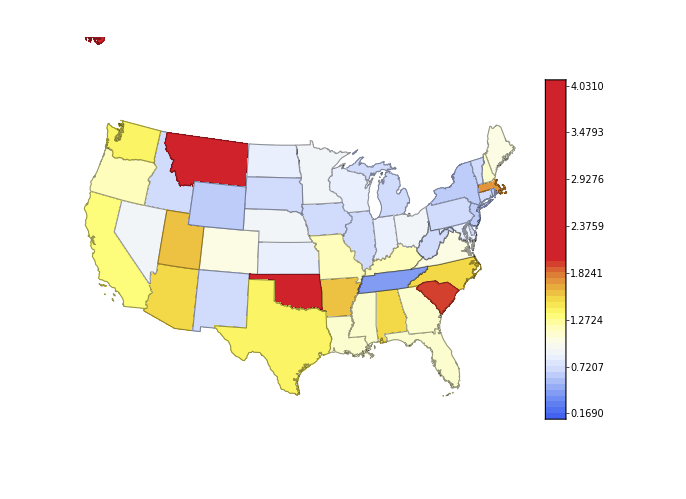

```mathematica
USMap = GeoRegionValuePlot[stateplotted,ImageSize->Large,ColorFunction->Function[{z},ColorData["TemperatureMap"][z/2]],ColorFunctionScaling->False,ImageSize->Full,GeoBackground->None, GeoRange->Quantity[2000,"Kilometers"],GeoCenter->Entity["AdministrativeDivision",{"Kansas","UnitedStates"}]]
stateMapFilename=NotebookDirectory[]<>"/results/SEIR-US-map-" <> DateString[{"ISODate"}] <> ".png";
Export[stateMapFilename, USMap, ImageResolution -> 600];
```

```mathematica
(* Export CSV files for visualising online *)
(* Data for US map *)
ExportR0 = Table[{i,ResultsPerState[[i]][[2]],ResultsPerState[[i]][[3]][[-(future+1)]][[2]]},{i,1,Length[ResultsPerState]}];
Export[NotebookDirectory[]<>"results/csv/US-r0.csv",ExportR0];
ExportInfected = Table[{i,ResultsPerState[[i]][[2]],ResultsPerState[[i]][[4]][[-(future+1)]][[2]]},{i,1,Length[ResultsPerState]}];
Export[NotebookDirectory[]<>"results/csv/US-active.csv",ExportInfected];
ExportRecovered = Table[{i,ResultsPerState[[i]][[2]],ResultsPerState[[i]][[5]][[-(future+1)]][[2]]},{i,1,Length[ResultsPerState]}];
Export[NotebookDirectory[]<>"results/csv/US-recovered.csv",ExportRecovered];
ExportDeaths = Table[{i,ResultsPerState[[i]][[2]],ResultsPerState[[i]][[6]][[-(future+1)]][[2]]},{i,1,Length[ResultsPerState]}];
Export[NotebookDirectory[]<>"results/csv/US-deaths.csv",ExportDeaths];
ExportCumulative = Table[{i,ResultsPerState[[i]][[2]],ResultsPerState[[i]][[7]][[-(future+1)]][[2]]},{i,1,Length[ResultsPerState]}];
Export[NotebookDirectory[]<>"results/csv/US-cumulative.csv",ExportCumulative];
ExportActiveDiff = Table[{i,ResultsPerState[[i]][[2]],ResultsPerState[[i]][[8]][[-(future+1)]][[2]]},{i,1,Length[ResultsPerState]}];
Export[NotebookDirectory[]<>"results/csv/US-active-diff.csv",ExportActiveDiff];
ExportDeathsDiff = Table[{i,ResultsPerState[[i]][[2]],ResultsPerState[[i]][[9]][[-(future+1)]][[2]]},{i,1,Length[ResultsPerState]}];
Export[NotebookDirectory[]<>"results/csv/US-deaths-diff.csv",ExportDeathsDiff];
ExportRisk = Table[{i,ResultsPerState[[i]][[2]],ResultsPerState[[i]][[11]][[-(future+1)]][[2]]},{i,1,Length[ResultsPerState]}];
Export[NotebookDirectory[]<>"results/csv/US-risk.csv",ExportRisk];

ExportCFR = Table[{i,ResultsPerState[[i]][[2]],ResultsPerState[[i]][[12]],ResultsPerState[[i]][[13]]},{i,1,Length[ResultsPerState]}];
Export[NotebookDirectory[]<>"results/csv/US-CFR.csv",ExportCFR];

(* Data per country *)
(* Name and ID *)
ExportList={};
For [country=1,country≤ Length[ResultsPerState],country++,
ExportList=Append[ExportList,{ResultsPerState[[country]][[1]],ResultsPerState[[country]][[2]]}]
]
Export[NotebookDirectory[]<>"results/csv/state-general.csv",ExportList];

(* Calculated data, one file per data series per country *)
ExportList={};
For [country=1,country≤ Length[ResultsPerState],country++,
Export[NotebookDirectory[]<>"results/csv/state-"<>ToString[country]<>"-r0.csv",ResultsPerState[[country]][[3]]];
Export[NotebookDirectory[]<>"results/csv/state-"<>ToString[country]<>"-i.csv",ResultsPerState[[country]][[4]]];
Export[NotebookDirectory[]<>"results/csv/state-"<>ToString[country]<>"-r.csv",ResultsPerState[[country]][[5]]];
Export[NotebookDirectory[]<>"results/csv/state-"<>ToString[country]<>"-m.csv",ResultsPerState[[country]][[6]]];
Export[NotebookDirectory[]<>"results/csv/state-"<>ToString[country]<>"-c.csv",ResultsPerState[[country]][[7]]];
Export[NotebookDirectory[]<>"results/csv/state-"<>ToString[country]<>"-di.csv",ResultsPerState[[country]][[8]]];
Export[NotebookDirectory[]<>"results/csv/state-"<>ToString[country]<>"-dm.csv",ResultsPerState[[country]][[9]]];
Export[NotebookDirectory[]<>"results/csv/state-"<>ToString[country]<>"-risk.csv",ResultsPerState[[country]][[11]]];
]
(* Data from Johns Hopkins, one file per data series per country *)
For [country=1,country≤ Length[ResultsPerState],country++,
Export[NotebookDirectory[]<>"results/csv/state-"<>ToString[country]<>"-jh-confirmed.csv",DataByState[[country]][[2]]];
Export[NotebookDirectory[]<>"results/csv/state-"<>ToString[country]<>"-jh-deaths.csv",DataByState[[country]][[3]]];
Export[NotebookDirectory[]<>"results/csv/state-"<>ToString[country]<>"-jh-confirmed-diff.csv",DataByState[[country]][[4]]];
Export[NotebookDirectory[]<>"results/csv/state-"<>ToString[country]<>"-jh-deaths-diff.csv",DataByState[[country]][[5]]];
]
```